# Buffon's Needle Problem

### Author

Eric W. Weisstein
December 13, 2005

This notebook downloaded from http://mathworld.wolfram.com/notebooks/ComputationalGeometry/BuffonsNeedleProblem.nb.

For more information, see Eric's MathWorld entry http://mathworld.wolfram.com/BuffonsNeedleProblem.html.

©2005 Wolfram Research, Inc. except for portions noted otherwise

## Analytic

### General

```mathematica
PDF[UniformDistribution[{0,d/2}],x]
```

Piecewise[{{2/d, 0≤x≤d/2}}]

```mathematica
PDF[UniformDistribution[{0,Pi/2}],q]
```

Piecewise[{{2/π, 0≤q≤π/2}}]

```mathematica
Assuming[{l>0,d>0,0<q<π/2},Simplify[∫_0^(π/2) (∫_0^(1/2 l sin(q)) 4/(π d)ⅆx)ⅆq]]
```

(2 l)/(d π)

```mathematica
Assuming[{l>0,d>0,0<q<π/2},Simplify[∫_0^(π/2) (∫_0^(1/2 l sin(q)) (2 Piecewise[({{2/d, 0≤x≤d/2}}),0])/π ⅆx)ⅆq]]
```

Piecewise[{{(2 l)/(d π), d≥l}, {(2 (l-√(-d^2+l^2)+d ArcCos[d/l]))/(d π), d<l}}]

```mathematica
FullSimplify[%/.l->x d,d>0]
```

Piecewise[{{(2 x)/π, x≤1}, {(2 (x-√(-1+x^2)+ArcSec[x]))/π, True}}]

## Probability Plot

```mathematica
Plot[Piecewise[{{(2x)/π,0≤x≤1},{(2 (x-√(x^2-1)+ ArcSec[x]))/π,x>1}}],{x,0,15},PlotStyle->Red,Epilog->{Blue,Dashing[{.02}],Line[{{1,0},{1,1}}]},
AxesLabel->TraditionalForm/@{x,P[x]}]
```

⁃Graphics⁃

## Visualization

```mathematica
BuffonsNeedle[r_,{x_,y_},n_]:=Block[
{data=Transpose[{Table[{x RandomReal[],y RandomReal[]},{n}],π Table[RandomReal[],{n}]}],
lines,hits,misses},
lines=(Function[s,First[#]+s  r/2 Through[{Cos,Sin}[Last[#]]]]/@{1,-1})&/@data;
{
Line[{{#,0},{#,y}}]&/@Range[0,Ceiling[x]],
PointSize[.01],
{misses,hits}=Map[Last,Split[Sort[Transpose[{Abs[Subtract@@(Floor/@First/@#)&/@lines],lines}]],(First[#1]==First[#2]&)],{2}];
Print["hits: ",Length[hits],"/",n," = ",N[100Length[hits]/n],"%, misses: ",Length[misses],"/",n," = ",N[100Length[misses]/n],"%,",Overscript[π,"^"]," = ",N[2n r/Length[hits]]];
Transpose[{
{Red,Green},
{Point/@Mean/@#,Line/@#}&/@{hits,misses}
}]
}
]
```

hits: 174/500 = 34.8%, misses: 326/500 = 65.2%,π̂ = 2.87356

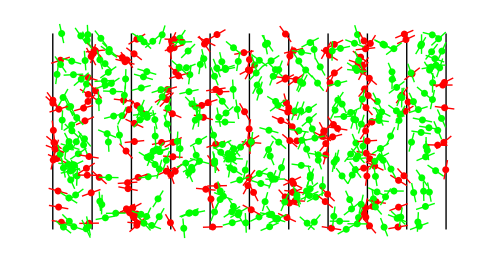

```mathematica
Show[Graphics[BuffonsNeedle[1/2,{10,5},500]],AspectRatio->Automatic,ImageSize->500]
```

```mathematica
With[{n=500,x=1/3},π^2/(2n)(π/x-2)]//N
```

0.0732796

hits: 65/100 = 65.%, misses: 35/100 = 35.%,π̂ = 2.8

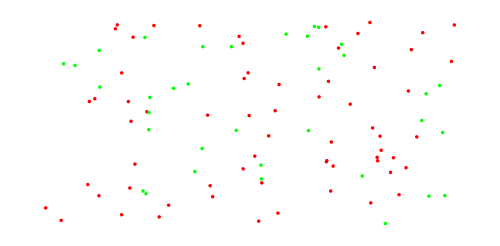
{0.,-Graphics-}

```mathematica
Show[Graphics[BuffonsNeedle[.91,{10,5},10^2]/.{l_Line:>{},p_PointSize:>PointSize[.005]}],AspectRatio->Automatic,ImageSize->500]//Timing
```